```mathematica
dimExpFactor[a_,b_]:=Log[4(1-Sqrt[1/2 -a -b])^2/(1/2 + a +b)]
```

```mathematica
a0=dimExpFactor[0,0];
```

```mathematica
firstDer=D[dimExpFactor[x,y],x]/.{x->0,y->0};
```

```mathematica
firstApprox[a_,b_]:=a0 + (a+b)firstDer
```

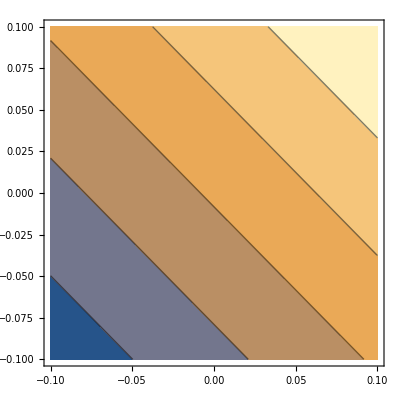

```mathematica
ContourPlot[firstApprox[x,y],{x,-0.1,0.1},{y,-0.1,0.1}]
```

```mathematica
conformalBlockPreFactor[Δ_,a_,b_]:=Exp[(Δ-1)dimExpFactor[a,b]]
SetOptions[RandomVariate,WorkingPrecision->100];
distributionsNatural[maxdim_,nZ_,sigmaz_]:=Table[{Table[dim,nZ],conformalBlockPreFactor[dim,RandomVariate[NormalDistribution[0,sigmaz],nZ],RandomVariate[NormalDistribution[0,sigmaz],nZ]]//Log},{dim,0,maxdim,2}];
distributionsRen[maxdim_,nZ_,sigmaz_]:=Table[{Table[dim,nZ],Exp[-(dim-1)dimExpFactor[0,0]]conformalBlockPreFactor[dim,RandomVariate[NormalDistribution[0,sigmaz],nZ],RandomVariate[NormalDistribution[0,sigmaz],nZ]]//Log},{dim,0,maxdim,2}];
```

```mathematica
plotsNat=ListPlot[distributionsNatural[16,100,1/1000][[#]]//Transpose]&/@Range[1,9];
Export["plot_sigma=e-4_noRen.pdf",Show[plotsNat,PlotRange->All]];
```

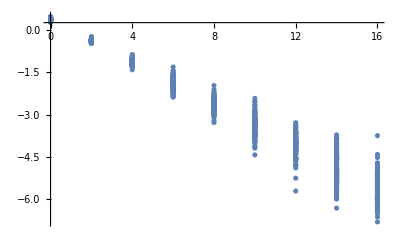

```mathematica
plotsNat=ListPlot[distributionsNatural[16,100,1/100][[#]]//Transpose]&/@Range[1,9];
Show[plotsNat,PlotRange->All]
Export["plot_sigma=e-3_noRen.pdf",Show[plotsNat,PlotRange->All]];
```

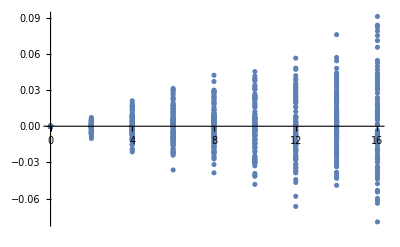

```mathematica
plotsRen=ListPlot[distributionsRen[16,100,1/1000][[#]]//Transpose]&/@Range[1,9];
Show[plotsRen,PlotRange->All]
Export["plot_sigma=e-4_Ren.pdf",Show[plotsRen,PlotRange->All]];
```

```mathematica
distributions[[1,2]]//Length
```

100

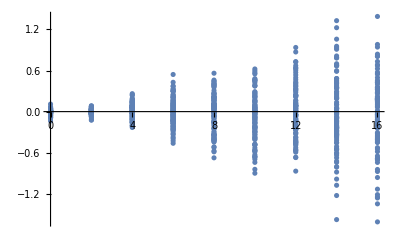

```mathematica
plotsRen=ListPlot[distributionsRen[16,100,1/100][[#]]//Transpose]&/@Range[1,9];
Show[plotsRen,PlotRange->All]
Export["plot_sigma=e-3_Ren.pdf",Show[plotsRen,PlotRange->All]];
```

```mathematica
.11
```